n-a Floor[n/a]

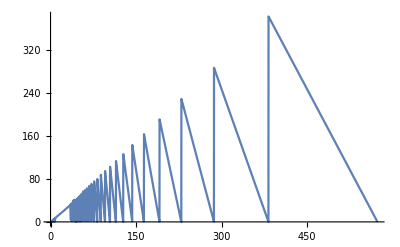

```mathematica
f[n_,a_]=n-(Floor[n/a]*a)
Plot[f[37*31,x],{x,0, 37*31/2}]
```

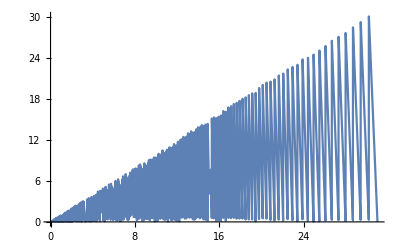

```mathematica
Plot[f[37*31,x],{x,0,31}]
```

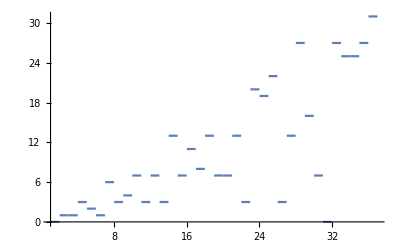

```mathematica
Plot[f[37*31,Floor[x]],{x,1,37}]
```

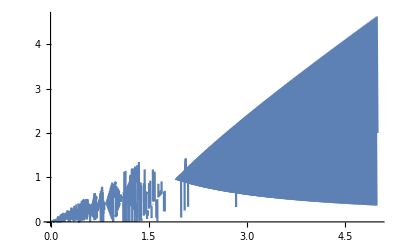

```mathematica
Plot[f[37*31,x],{x,0,5}]
```

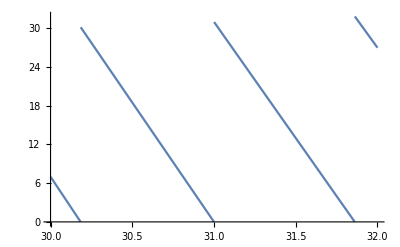

```mathematica
Plot[f[37*31,x],{x,30,32}]
```

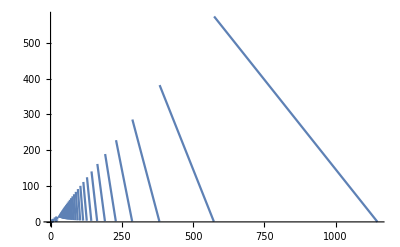

```mathematica
Plot[f[37*31,x],{x,0,31*37}]
```

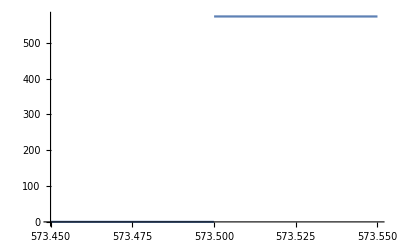

```mathematica
Plot[f[37*31,x],{x,573.45,573.55}]
```

```mathematica
N[37*31/573.5]
```

2.

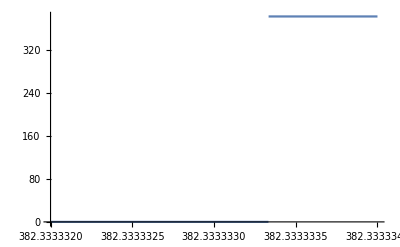

```mathematica
Plot[f[37*31,x],{x,382.333332,382.333334}]
```

```mathematica
N[37*31/382.333333333]
```

3.

```mathematica
N[537.5/382.333333333]
```

1.40584

```mathematica
N[537.5-382.333333333]
```

155.167

n/x

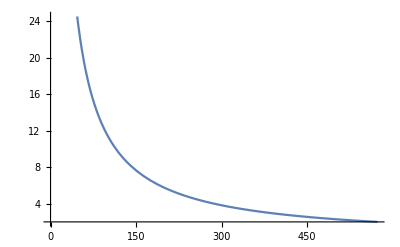

```mathematica
g[n_,x_]=n/x
Plot[g[37*31,x],{x,0, 37*31/2}]
```

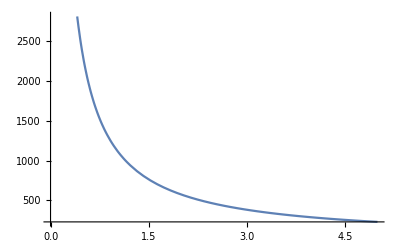

```mathematica
Plot[g[37*31,x],{x,0, 5}]
```

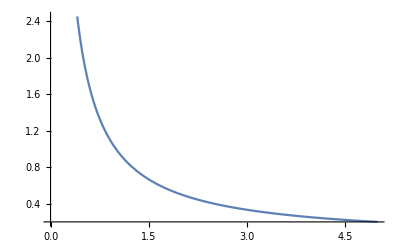

```mathematica
Plot[1/x,{x,0,5}]
```

```mathematica
D[1/x,x]
```

-1/x^2

```mathematica
D[g[37*31,x],x]
```

-1147/x^2

```mathematica
Solve[-1147/x^2==-1,x]
```

{{x→-√1147},{x→√1147}}

```mathematica
n-(Floor[n/a]*a)
Solve[f[37*31/a]==Floor[x]
```

```mathematica
Solve[DiracComb[x]==+Infinity,x]
```

Solve::infc: The system DiracComb[x]==∞ contains an infinite object ∞.

Solve[DiracComb[x]==∞,x]

```mathematica
DiracComb[1]
```

DiracComb[1]

```mathematica
comb[t_,T_]=1/T*Sum[E^(I*2*Pi*n*(t/T)),{n,-Infinity,+Infinity}]
```

Sum::div: Sum does not converge.

(∑_(n=-∞)^∞ ⅇ^((2 ⅈ n π t)/T))/T

```mathematica
comb[t,1]
```

Sum::div: Sum does not converge.

∑_(n=-∞)^∞ ⅇ^(2 ⅈ n π t)

```mathematica
comb[x,1]
```

Sum::div: Sum does not converge.

∑_(n=-∞)^∞ ⅇ^(2 ⅈ n π x)

```mathematica
Plot[N[comb[x,1]],{x,0,2}]
```

Sum::div: Sum does not converge.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in n near {n} = {4.81037×10^7}. NIntegrate obtained 3853.13+6777.97 ⅈ and 14746.9 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in n near {n} = {-4.81037×10^7}. NIntegrate obtained -3851.39+6778.96 ⅈ and 14746.9 for the integral and error estimates.